# AllContractions

Some notes on the AllContractions function.

```mathematica
DateString[]
```

Sun 8 Jun 2014 22:25:51

### Setup

```mathematica
<<xAct`xTras`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.1, {2014,2,15}

CopyRight (C) 2003-2014, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.0, {2014,2,23}

CopyRight (C) 2002-2014, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xPert`  version 1.0.4, {2014,2,15}

CopyRight (C) 2005-2014, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2014,2,15}

CopyRight (C) 2006-2014, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.1, {2014,2,15}

CopyRight (C) 2005-2014, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.0, {2014,1,24}

CopyRight (C) 2011-2014, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.3.3.6, {2014,6,5}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
DefManifold[M,4,IndexRange[a,l]]
```

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

```mathematica
DefMetric[-1,metric[-a,-b],CD,PrintAs->"g",CurvatureRelations->False]
```

** DefTensor: Defining symmetric metric tensor metric[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilonmetric[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetrametric[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetrametric†[-a,-b,-c,-d].

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCD[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor RicciCD[-a,-b].

** DefTensor: Defining Ricci scalar RicciScalarCD[].

** DefTensor: Defining symmetric Einstein tensor EinsteinCD[-a,-b].

** DefTensor: Defining Weyl tensor WeylCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCD[-a,-b].

** DefTensor: Defining Kretschmann scalar KretschmannCD[].

** DefCovD:  Computing RiemannToWeylRules for dim 4

** DefCovD:  Computing RicciToTFRicci for dim 4

** DefCovD:  Computing RicciToEinsteinRules for dim 4

** DefTensor: Defining symmetrized Riemann tensor SymRiemannCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric Schouten tensor SchoutenCD[-a,-b].

** DefTensor: Defining symmetric cosmological Schouten tensor SchoutenCCCD[LI[_],-a,-b].

** DefTensor: Defining symmetric cosmological Einstein tensor EinsteinCCCD[LI[_],-a,-b].

** DefTensor: Defining weight +2 density Detmetric[]. Determinant.

** DefParameter: Defining parameter PerturbationParametermetric.

** DefTensor: Defining tensor Perturbationmetric[LI[order],-a,-b].

```mathematica
PrintAs[RiemannCD]^="R";
PrintAs[RicciCD]^="R";
PrintAs[RicciScalarCD]^="R";
```

### Metric coset approach

We want to compute all contractions of two Riemann tensors:

```mathematica
riemannsquared=RiemannCD[-a,-b,-c,-d]RiemannCD[-e,-f,-g,-h]
```

R |   |   |   |  
a | b | c | d R |   |   |   |  
e | f | g | h

```mathematica
7!!
```

105

This amounts to an enumeration of the double cosets of H \ S_8/ G, with H=sym(R^2) and G=sym(g^4).
We have |G| = 2^4 4! = 384 and |H| = 8^2 2! = 128.
Furthermore, |S_8/G | = 105 and |S_8/H | = 315.

A straightforward way to compute all contractions is to first enumerate all index configurations g^(<ab)g^cd g^ef g^(gh>) (where the <> brackets denote all independent index configurations, of which there are 105), contract those with R_abcd R_efgh, and then canonicalize the contractions and delete duplicates afterwards.

```mathematica
metrics=metric[a,b]metric[c,d]metric[e,f]metric[g,h]
```

g | a | b
  |   g | c | d
  |   g | e | f
  |   g | g | h
  |

```mathematica
metricsindexconfigs = IndexConfigurations[metrics];
metricsindexconfigs//Length
```

105

```mathematica
contractions =metricsindexconfigs riemannsquared // ContractMetric//ToCanonical //SameDummies// Union
```

{0,-R |   |   |   |  
a | b | c | d R | a | b | c | d
  |   |   |  ,R |   |   |   |  
a | b | c | d R | a | b | c | d
  |   |   |  ,-R |   |   |   |  
a | c | b | d R | a | b | c | d
  |   |   |  ,R |   |   |   |  
a | c | b | d R | a | b | c | d
  |   |   |  ,-R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d,R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d,-R | a | b |   |  
  |   | a | b R | c | d |   |  
  |   | c | d,R | a | b |   |  
  |   | a | b R | c | d |   |  
  |   | c | d}

We still need to remove overall signs and zeros.

```mathematica
RemoveSignsAndZeros[0]:=Sequence[];
RemoveSignsAndZeros[x_]:=x;
RemoveSignsAndZeros[-x_]:=x;
SetAttributes[RemoveSignsAndZeros,Listable]
```

```mathematica
contractions=contractions//RemoveSignsAndZeros//Union
```

{R |   |   |   |  
a | b | c | d R | a | b | c | d
  |   |   |  ,R |   |   |   |  
a | c | b | d R | a | b | c | d
  |   |   |  ,R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d,R | a | b |   |  
  |   | a | b R | c | d |   |  
  |   | c | d}

So, there are only 4 independent contractions. Using  g^(<ab)g^cd g^ef g^(gh>) to arrive at these contractions then seems a bit of an overkill, since we need to call the canonicalizer 105 times. Is there a better way?

### Iterative approach I

#### Function definitions

Another way is to iteratively take all single contractions of an expression and canonicalize those, repeated until we end up with a scalar.

Here' s a series of functions that takes all possible single contractions :

```mathematica
SingleMetrics[expr_]:=
(* Create list of all possible single metrics that contract one pair of the free indices of expr. *)
metric@@@Subsets[ChangeIndex/@IndicesOf[Free][expr],{2}];
```

```mathematica
SingleMetrics[riemannsquared]
```

{g | a | b
  |  ,g | a | c
  |  ,g | a | d
  |  ,g | a | e
  |  ,g | a | f
  |  ,g | a | g
  |  ,g | a | h
  |  ,g | b | c
  |  ,g | b | d
  |  ,g | b | e
  |  ,g | b | f
  |  ,g | b | g
  |  ,g | b | h
  |  ,g | c | d
  |  ,g | c | e
  |  ,g | c | f
  |  ,g | c | g
  |  ,g | c | h
  |  ,g | d | e
  |  ,g | d | f
  |  ,g | d | g
  |  ,g | d | h
  |  ,g | e | f
  |  ,g | e | g
  |  ,g | e | h
  |  ,g | f | g
  |  ,g | f | h
  |  ,g | g | h
  |  }

```mathematica
SingleContractions[expr_]:=
(* Contract separate metrics and change the free indices to be uniform. *)
With[{frees=List@@IndicesOf[Free][expr]},
Map[
ToCanonical @ ContractMetric @ ChangeFreeIndices[#,frees[[1;;-3]]]&,
SingleMetrics[expr]expr
]
];
```

```mathematica
SingleContractions[riemannsquared]
```

{0,R |   | g |   |  
a |   | b | g R |   |   |   |  
c | d | e | f,-R |   | g |   |  
a |   | b | g R |   |   |   |  
c | d | e | f,R |   | g |   |  
a |   | b | c R |   |   |   |  
d | g | e | f,-R |   | g |   |  
a |   | b | c R |   |   |   |  
d | g | e | f,R |   | g |   |  
a |   | b | c R |   |   |   |  
d | e | f | g,-R |   | g |   |  
a |   | b | c R |   |   |   |  
d | e | f | g,-R |   | g |   |  
a |   | b | g R |   |   |   |  
c | d | e | f,R |   | g |   |  
a |   | b | g R |   |   |   |  
c | d | e | f,-R |   | g |   |  
a |   | b | c R |   |   |   |  
d | g | e | f,R |   | g |   |  
a |   | b | c R |   |   |   |  
d | g | e | f,-R |   | g |   |  
a |   | b | c R |   |   |   |  
d | e | f | g,R |   | g |   |  
a |   | b | c R |   |   |   |  
d | e | f | g,0,R |   |   |   | g
a | b | c |   R |   |   |   |  
d | g | e | f,-R |   |   |   | g
a | b | c |   R |   |   |   |  
d | g | e | f,R |   |   |   | g
a | b | c |   R |   |   |   |  
d | e | f | g,-R |   |   |   | g
a | b | c |   R |   |   |   |  
d | e | f | g,-R |   |   |   | g
a | b | c |   R |   |   |   |  
d | g | e | f,R |   |   |   | g
a | b | c |   R |   |   |   |  
d | g | e | f,-R |   |   |   | g
a | b | c |   R |   |   |   |  
d | e | f | g,R |   |   |   | g
a | b | c |   R |   |   |   |  
d | e | f | g,0,R |   |   |   |  
a | b | c | d R |   | g |   |  
e |   | f | g,-R |   |   |   |  
a | b | c | d R |   | g |   |  
e |   | f | g,-R |   |   |   |  
a | b | c | d R |   | g |   |  
e |   | f | g,R |   |   |   |  
a | b | c | d R |   | g |   |  
e |   | f | g,0}

```mathematica
UniqueSingleContractions[expr_]:=
(* Remove duplicates, make dummies equal, and take a union. *)
Union @ ScreenDollarIndices @ ReplaceDummies @ RemoveSignsAndZeros @ SingleContractions[expr];
```

#### Computing contractions

The first single contractions are then:

```mathematica
firstcontractions=UniqueSingleContractions[riemannsquared]
```

{R |   | g |   |  
a |   | b | g R |   |   |   |  
c | d | e | f,R |   |   |   | g
a | b | c |   R |   |   |   |  
d | e | f | g,R |   | g |   |  
a |   | b | c R |   |   |   |  
d | e | f | g,R |   |   |   | g
a | b | c |   R |   |   |   |  
d | g | e | f,R |   | g |   |  
a |   | b | c R |   |   |   |  
d | g | e | f,R |   |   |   |  
a | b | c | d R |   | g |   |  
e |   | f | g}

Ok, now compute the second contractions:

```mathematica
secondcontractions = UniqueSingleContractions/@firstcontractions
secondcontractionsflattened = Union@@secondcontractions
```

{{R |   | f |   |  
a |   | e | f R |   |   |   | e
b | c | d |  ,R |   | f |   |  
a |   | e | f R |   | e |   |  
b |   | c | d,R |   | e |   |  
a |   | b | e R |   | f |   |  
c |   | d | f,R |   |   |   |  
a | b | c | d R | e | f |   |  
  |   | e | f},{R |   | f |   |  
a |   | e | f R |   |   |   | e
b | c | d |  ,R |   |   | e | f
a | b |   |   R |   |   |   |  
c | d | e | f,R |   | e |   | f
a |   | b |   R |   |   |   |  
c | d | e | f,R |   |   | e | f
a | b |   |   R |   |   |   |  
c | e | d | f,R |   | e |   | f
a |   | b |   R |   |   |   |  
c | e | d | f,R |   |   |   | e
a | b | c |   R |   | f |   |  
d |   | e | f},{R |   | f |   |  
a |   | e | f R |   |   |   | e
b | c | d |  ,R |   |   | e | f
a | b |   |   R |   |   |   |  
c | d | e | f,R |   | e |   | f
a |   | b |   R |   |   |   |  
c | d | e | f,R |   |   | e | f
a | b |   |   R |   |   |   |  
c | e | d | f,R |   | e |   | f
a |   | b |   R |   |   |   |  
c | f | d | e,R |   | e |   |  
a |   | b | c R |   | f |   |  
d |   | e | f},{R |   | f |   |  
a |   | e | f R |   | e |   |  
b |   | c | d,R |   |   | e | f
a | b |   |   R |   |   |   |  
c | d | e | f,R |   | e |   | f
a |   | b |   R |   |   |   |  
c | d | e | f,R |   |   | e | f
a | b |   |   R |   |   |   |  
c | e | d | f,R |   | e |   | f
a |   | b |   R |   |   |   |  
c | f | d | e,R |   |   |   | e
a | b | c |   R |   | f |   |  
d |   | e | f},{R |   | f |   |  
a |   | e | f R |   | e |   |  
b |   | c | d,R |   |   | e | f
a | b |   |   R |   |   |   |  
c | d | e | f,R |   | e |   | f
a |   | b |   R |   |   |   |  
c | d | e | f,R |   |   | e | f
a | b |   |   R |   |   |   |  
c | e | d | f,R |   | e |   | f
a |   | b |   R |   |   |   |  
c | e | d | f,R |   | e |   |  
a |   | b | c R |   | f |   |  
d |   | e | f},{R |   | e |   |  
a |   | b | e R |   | f |   |  
c |   | d | f,R |   |   |   | e
a | b | c |   R |   | f |   |  
d |   | e | f,R |   | e |   |  
a |   | b | c R |   | f |   |  
d |   | e | f,R |   |   |   |  
a | b | c | d R | e | f |   |  
  |   | e | f}}

{R |   | f |   |  
a |   | e | f R |   |   |   | e
b | c | d |  ,R |   | f |   |  
a |   | e | f R |   | e |   |  
b |   | c | d,R |   |   | e | f
a | b |   |   R |   |   |   |  
c | d | e | f,R |   | e |   | f
a |   | b |   R |   |   |   |  
c | d | e | f,R |   |   | e | f
a | b |   |   R |   |   |   |  
c | e | d | f,R |   | e |   | f
a |   | b |   R |   |   |   |  
c | e | d | f,R |   | e |   | f
a |   | b |   R |   |   |   |  
c | f | d | e,R |   | e |   |  
a |   | b | e R |   | f |   |  
c |   | d | f,R |   |   |   | e
a | b | c |   R |   | f |   |  
d |   | e | f,R |   | e |   |  
a |   | b | c R |   | f |   |  
d |   | e | f,R |   |   |   |  
a | b | c | d R | e | f |   |  
  |   | e | f}

And so on until we end up with scalars:

```mathematica
thirdcontractions = UniqueSingleContractions/@secondcontractionsflattened
thirdcontractionsflattened = Union@@thirdcontractions
```

{{R |   | c |   | d
a |   | c |   R |   | e |   |  
b |   | d | e,R |   | c |   | d
a |   | b |   R |   | e |   |  
c |   | d | e},{R |   | c |   | d
a |   | c |   R |   | e |   |  
b |   | d | e,R |   | c |   | d
a |   | b |   R |   | e |   |  
c |   | d | e},{R |   | c | d | e
a |   |   |   R |   |   |   |  
b | c | d | e},{R |   | c | d | e
a |   |   |   R |   |   |   |  
b | d | c | e},{R |   | c | d | e
a |   |   |   R |   |   |   |  
b | d | c | e},{R |   | c | d | e
a |   |   |   R |   |   |   |  
b | c | d | e,R |   | c | d | e
a |   |   |   R |   |   |   |  
b | d | c | e,R |   | c |   | d
a |   | b |   R |   | e |   |  
c |   | d | e},{R |   | c | d | e
a |   |   |   R |   |   |   |  
b | c | d | e,R |   | c | d | e
a |   |   |   R |   |   |   |  
b | d | c | e,R |   | c |   | d
a |   | b |   R |   | e |   |  
c |   | d | e},{R |   | c |   | d
a |   | c |   R |   | e |   |  
b |   | d | e,R |   | c |   |  
a |   | b | c R | d | e |   |  
  |   | d | e},{R |   | c |   | d
a |   | c |   R |   | e |   |  
b |   | d | e,R |   | c |   | d
a |   | b |   R |   | e |   |  
c |   | d | e},{R |   | c |   | d
a |   | c |   R |   | e |   |  
b |   | d | e,R |   | c |   | d
a |   | b |   R |   | e |   |  
c |   | d | e},{R |   | c |   |  
a |   | b | c R | d | e |   |  
  |   | d | e}}

{R |   | c | d | e
a |   |   |   R |   |   |   |  
b | c | d | e,R |   | c | d | e
a |   |   |   R |   |   |   |  
b | d | c | e,R |   | c |   | d
a |   | c |   R |   | e |   |  
b |   | d | e,R |   | c |   | d
a |   | b |   R |   | e |   |  
c |   | d | e,R |   | c |   |  
a |   | b | c R | d | e |   |  
  |   | d | e}

```mathematica
fourthcontractions = UniqueSingleContractions/@thirdcontractionsflattened
fourthcontractionsflattened = Union@@fourthcontractions
```

{{R |   |   |   |  
a | b | c | d R | a | b | c | d
  |   |   |  },{R |   |   |   |  
a | c | b | d R | a | b | c | d
  |   |   |  },{R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d},{R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d},{R | a | b |   |  
  |   | a | b R | c | d |   |  
  |   | c | d}}

{R |   |   |   |  
a | b | c | d R | a | b | c | d
  |   |   |  ,R |   |   |   |  
a | c | b | d R | a | b | c | d
  |   |   |  ,R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d,R | a | b |   |  
  |   | a | b R | c | d |   |  
  |   | c | d}

We end up with the same contractions as in the previous section:

```mathematica
contractions==fourthcontractionsflattened
```

True

#### Contractions graph

But we haven’t been very efficient. Take a look at the tree graph that takes the fully uncontracted expression to the four scalars; each edge represents a single contraction:

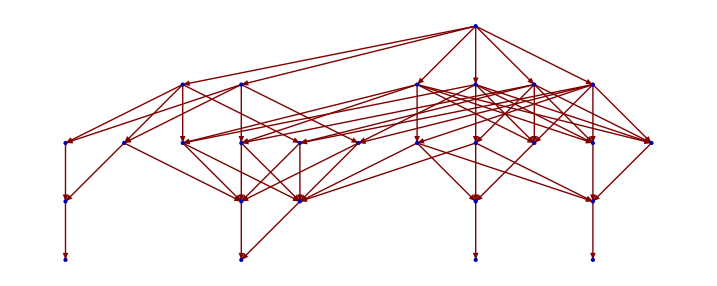

```mathematica
graph1=Thread/@{
{riemannsquared}->{firstcontractions},
firstcontractions->secondcontractions,
secondcontractionsflattened->thirdcontractions,
thirdcontractionsflattened->fourthcontractions
}/.rule_Rule:>Thread[rule]//Flatten ;
graph1//LayeredGraphPlot
```

That’s a lot of redundant edges. But also a lot of redundant vertices. Take for instances the first contractions,

```mathematica
firstcontractions
```

{R |   | g |   |  
a |   | b | g R |   |   |   |  
c | d | e | f,R |   |   |   | g
a | b | c |   R |   |   |   |  
d | e | f | g,R |   | g |   |  
a |   | b | c R |   |   |   |  
d | e | f | g,R |   |   |   | g
a | b | c |   R |   |   |   |  
d | g | e | f,R |   | g |   |  
a |   | b | c R |   |   |   |  
d | g | e | f,R |   |   |   |  
a | b | c | d R |   | g |   |  
e |   | f | g}

We have 6 of those, while we only need the first two, namely R_ab R_cdef and R_abc^g R_defg. These are respectively the first vertex on the first depth, and the third vertex on the first depth. It is obvious by looking at the above graph that you can still reach the bottom four vertices if we delete the other vertices on the first depth.

#### Reduced contractions graph

Let’s see this explicitly:

```mathematica
requiredfirstcontractions = firstcontractions[[1;;2]]
```

{R |   | g |   |  
a |   | b | g R |   |   |   |  
c | d | e | f,R |   |   |   | g
a | b | c |   R |   |   |   |  
d | e | f | g}

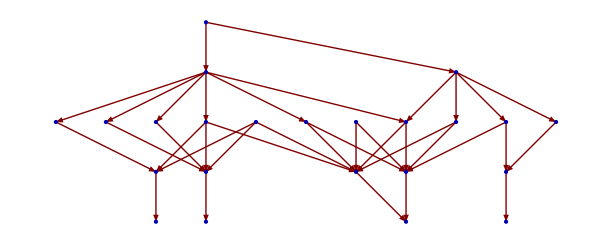

```mathematica
graph2=Select[
graph1,
FreeQ[#,Alternatives@@Complement[firstcontractions,requiredfirstcontractions]]&
];
graph2//LayeredGraphPlot
```

Ok, so we can’t reach two vertices on the second depth, but that’s okay: we don’t need them to reach the bottom four vertices.

We could repeat this procedure for the second depth to obtain a minimal tree, but instead we’ll now jump to an algorithm that generates it automatically.

### Iterative approach II

#### Properties of required contractions

What is a defining property of the required first contractions? Let’s look at them in more detail:

```mathematica
requiredfirstcontractions
```

{R |   | g |   |  
a |   | b | g R |   |   |   |  
c | d | e | f,R |   |   |   | g
a | b | c |   R |   |   |   |  
d | e | f | g}

```mathematica
Complement[firstcontractions,requiredfirstcontractions]
```

{R |   | g |   |  
a |   | b | c R |   |   |   |  
d | e | f | g,R |   |   |   | g
a | b | c |   R |   |   |   |  
d | g | e | f,R |   | g |   |  
a |   | b | c R |   |   |   |  
d | g | e | f,R |   |   |   |  
a | b | c | d R |   | g |   |  
e |   | f | g}

We can generate the others from the required first contractions by considering all permutations of the free indices:

```mathematica
firstfreeindices= List@@IndicesOf[Free][requiredfirstcontractions];
```

```mathematica
freepermuterules=Thread[firstfreeindices->#]&/@Permutations@firstfreeindices;
```

```mathematica
requiredfirstcontractions/.freepermuterules//Flatten//ToCanonical//RemoveSignsAndZeros//Union;
Select[%,OrderedQ[FindIndices[Evaluate@#]/.-g|g->Sequence[]]&]
```

{R |   | g |   |  
a |   | b | g R |   |   |   |  
c | d | e | f,R |   |   |   | g
a | b | c |   R |   |   |   |  
d | e | f | g,R |   | g |   |  
a |   | b | c R |   |   |   |  
d | e | f | g,R |   |   |   | g
a | b | c |   R |   |   |   |  
d | g | e | f,R |   | g |   |  
a |   | b | c R |   |   |   |  
d | g | e | f,R |   |   |   |  
a | b | c | d R |   | g |   |  
e |   | f | g}

So if we consider the free indices the be orderless (that is, we are allowed to interchange them freely) the set of first contractions reduces to just the required first contractions.

#### Canonicalization of orderless free indices

We implement the orderlessness of the free indices with a ‘hack’: we first set all free indices to the same c-index, canonicalize, and then re-insert the free indices. 

Note that we have to be a bit careful with antisymmetric permutations in the underlying SGS when doing this, because repeated c-indices are symmetric.

Ok, so first introduces a basis to get a valid c-index.

```mathematica
DefBasis[B,TangentM,{0,1,2,3}]
```

** DefBasis: Defining basis B.

** DefCovD: Defining parallel derivative PDB[-a].

** DefTensor: Defining torsion tensor TorsionPDB[a,-b,-c].

** DefTensor: Defining non-symmetric Christoffel tensor ChristoffelPDB[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDB[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDB[-a,-b].

** DefTensor: Defining antisymmetric +1 density etaUpB[a,b,c,d].

** DefTensor: Defining antisymmetric -1 density etaDownB[-a,-b,-c,-d].

The canonicalization with orderless free indices then goes as follows:

```mathematica
expr=firstcontractions//Last
```

R |   |   |   |  
a | b | c | d R |   | g |   |  
e |   | f | g

```mathematica
frees= List@@IndicesOf[Free][expr]
```

{-a,-b,-c,-d,-e,-f}

```mathematica
exprnofrees=expr/.(#->{0,-B}&/@frees)
```

R |   | g |   |  
0 |   | 0 | g R |   |   |   |  
0 | 0 | 0 | 0

```mathematica
ToCanonical[exprnofrees]
```

0

See, we had to be a bit careful with antisymmetric permutations in the underlying SGS (in this case, that of the Riemann tensor).

```mathematica
oldsym=SymmetryGroupOfTensor[RiemannCD]
```

StrongGenSet[{1,2,3,4},GenSet[(1,3)(2,4),-(1,2),-(3,4)]]

```mathematica
SymmetryGroupOfTensor[RiemannCD]^=oldsym/.-c_Cycles:>c
```

StrongGenSet[{1,2,3,4},GenSet[(1,2),(3,4),(1,3)(2,4)]]

```mathematica
exprnofreescanon=ToCanonical[exprnofrees]
```

R | g |   |   |  
  | 0 | g | 0 R |   |   |   |  
0 | 0 | 0 | 0

```mathematica
counter=0;
exprwithfrees = exprnofreescanon/.{0,-B}:>(frees[[++counter]])
```

R |   |   |   |  
c | d | e | f R | g |   |   |  
  | a | g | b

```mathematica
SymmetryGroupOfTensor[RiemannCD]^=oldsym
```

StrongGenSet[{1,2,3,4},GenSet[(1,3)(2,4),-(1,2),-(3,4)]]

```mathematica
exprfinal = ToCanonical[exprwithfrees]
```

R |   | g |   |  
a |   | b | g R |   |   |   |  
c | d | e | f

We gather the above in the following function:

```mathematica
CanonicalizeOrderlessFrees[expr_]:=
Module[{
oldsym = SymmetryGroupOfTensor[RiemannCD],
frees = List@@IndicesOf[Free][expr],
counter=0,
result
},
SymmetryGroupOfTensor[RiemannCD]^=oldsym/.-c_Cycles:>c;
result=ToCanonical[expr/.(#->{0,-B}&/@frees)];
result=result/.{0,-B}:>(frees[[++counter]]);
SymmetryGroupOfTensor[RiemannCD]^=oldsym;
ToCanonical@result
];
SetAttributes[CanonicalizeOrderlessFrees,Listable]
```

The first contractions now reduce to two contractions (that are not exactly the same as the previous required contractions, but an equivalent set):

```mathematica
firstcontractions
CanonicalizeOrderlessFrees/@%
```

{R |   | g |   |  
a |   | b | g R |   |   |   |  
c | d | e | f,R |   |   |   | g
a | b | c |   R |   |   |   |  
d | e | f | g,R |   | g |   |  
a |   | b | c R |   |   |   |  
d | e | f | g,R |   |   |   | g
a | b | c |   R |   |   |   |  
d | g | e | f,R |   | g |   |  
a |   | b | c R |   |   |   |  
d | g | e | f,R |   |   |   |  
a | b | c | d R |   | g |   |  
e |   | f | g}

{R |   | g |   |  
a |   | b | g R |   |   |   |  
c | d | e | f,R |   | g |   |  
a |   | b | c R |   |   |   |  
d | g | e | f,R |   | g |   |  
a |   | b | c R |   |   |   |  
d | g | e | f,R |   | g |   |  
a |   | b | c R |   |   |   |  
d | g | e | f,R |   | g |   |  
a |   | b | c R |   |   |   |  
d | g | e | f,R |   | g |   |  
a |   | b | g R |   |   |   |  
c | d | e | f}

```mathematica
Union[%]
```

{R |   | g |   |  
a |   | b | g R |   |   |   |  
c | d | e | f,R |   | g |   |  
a |   | b | c R |   |   |   |  
d | g | e | f}

#### Computing contractions

Let’s redefine the function SingleContractions from the previous section, changing only the call to ToCanonical to CanonicalizeOrderlessFrees:

```mathematica
SingleContractions[expr_]:=
(* Contract separate metrics and change the free indices to be uniform. *)
With[{frees=List@@IndicesOf[Free][expr]},
Map[
CanonicalizeOrderlessFrees @ ContractMetric @ ChangeFreeIndices[#,frees[[1;;-3]]]&,
SingleMetrics[expr]expr
]
];
```

We can now again iteratively take contractions in order to end up with scalars:

```mathematica
firstcontractions=UniqueSingleContractions[riemannsquared]
```

{R |   | g |   |  
a |   | b | g R |   |   |   |  
c | d | e | f,R |   | g |   |  
a |   | b | c R |   |   |   |  
d | g | e | f}

```mathematica
secondcontractions = UniqueSingleContractions/@firstcontractions
secondcontractionsflattened = Union@@secondcontractions
```

{{R |   | f |   |  
a |   | e | f R |   | e |   |  
b |   | c | d,R |   | e |   |  
a |   | b | e R |   | f |   |  
c |   | d | f,R |   |   |   |  
a | b | c | d R | e | f |   |  
  |   | e | f},{R |   | f |   |  
a |   | e | f R |   | e |   |  
b |   | c | d,R |   |   | e | f
a | b |   |   R |   |   |   |  
c | d | e | f,R |   | e |   | f
a |   | b |   R |   |   |   |  
c | d | e | f,R |   | e |   | f
a |   | b |   R |   |   |   |  
c | e | d | f}}

{R |   | f |   |  
a |   | e | f R |   | e |   |  
b |   | c | d,R |   |   | e | f
a | b |   |   R |   |   |   |  
c | d | e | f,R |   | e |   | f
a |   | b |   R |   |   |   |  
c | d | e | f,R |   | e |   | f
a |   | b |   R |   |   |   |  
c | e | d | f,R |   | e |   |  
a |   | b | e R |   | f |   |  
c |   | d | f,R |   |   |   |  
a | b | c | d R | e | f |   |  
  |   | e | f}

```mathematica
thirdcontractions = UniqueSingleContractions/@secondcontractionsflattened
thirdcontractionsflattened = Union@@thirdcontractions
```

{{R |   | c |   | d
a |   | c |   R |   | e |   |  
b |   | d | e,R |   | c |   | d
a |   | b |   R |   | e |   |  
c |   | d | e},{R |   | c | d | e
a |   |   |   R |   |   |   |  
b | c | d | e},{R |   | c | d | e
a |   |   |   R |   |   |   |  
b | d | c | e},{R |   | c | d | e
a |   |   |   R |   |   |   |  
b | c | d | e,R |   | c | d | e
a |   |   |   R |   |   |   |  
b | d | c | e,R |   | c |   | d
a |   | b |   R |   | e |   |  
c |   | d | e},{R |   | c |   | d
a |   | c |   R |   | e |   |  
b |   | d | e,R |   | c |   |  
a |   | b | c R | d | e |   |  
  |   | d | e},{R |   | c |   |  
a |   | b | c R | d | e |   |  
  |   | d | e}}

{R |   | c | d | e
a |   |   |   R |   |   |   |  
b | c | d | e,R |   | c | d | e
a |   |   |   R |   |   |   |  
b | d | c | e,R |   | c |   | d
a |   | c |   R |   | e |   |  
b |   | d | e,R |   | c |   | d
a |   | b |   R |   | e |   |  
c |   | d | e,R |   | c |   |  
a |   | b | c R | d | e |   |  
  |   | d | e}

```mathematica
fourthcontractions = UniqueSingleContractions/@thirdcontractionsflattened
fourthcontractionsflattened = Union@@fourthcontractions
```

{{R |   |   |   |  
a | b | c | d R | a | b | c | d
  |   |   |  },{R |   |   |   |  
a | c | b | d R | a | b | c | d
  |   |   |  },{R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d},{R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d},{R | a | b |   |  
  |   | a | b R | c | d |   |  
  |   | c | d}}

{R |   |   |   |  
a | b | c | d R | a | b | c | d
  |   |   |  ,R |   |   |   |  
a | c | b | d R | a | b | c | d
  |   |   |  ,R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d,R | a | b |   |  
  |   | a | b R | c | d |   |  
  |   | c | d}

We end up with the same contractions as in the previous section:

```mathematica
contractions==fourthcontractionsflattened
```

True

#### Contractions graph

We’re now much more efficient in terms of generated intermediate contractions:

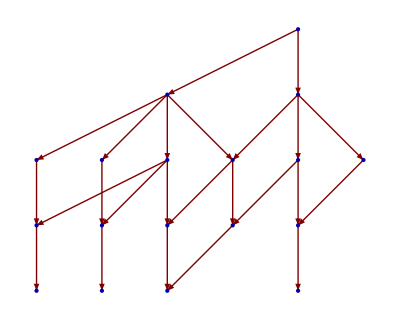

```mathematica
graph3=Thread/@{
{riemannsquared}->{firstcontractions},
firstcontractions->secondcontractions,
secondcontractionsflattened->thirdcontractions,
thirdcontractionsflattened->fourthcontractions
}/.rule_Rule:>Thread[rule]//Flatten ;
graph3//LayeredGraphPlot
```

Compare this to the original graph from the previous section:

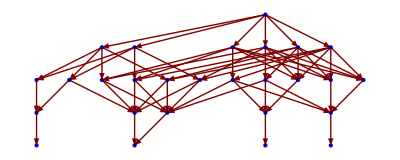

```mathematica
graph1//LayeredGraphPlot
```

```mathematica
Length/@{graph1,graph3}
```

{63,24}

We have reduced the complexity of the contractions graph, at the expense of a double call to ToCanonical for the canonicalization of each contraction. It would be nice if the effective functionality of CanonicalizeOrderlessFrees could be integrated into xperm.c.

### Iterative approach III

It is much more efficient to work directly in terms of permutations than tensorial expressions, since then ToCanonical doesn’t have to digest the expressions before calling the relevant xPerm function to do the canonicalization.

TO BE CONTINUED ....